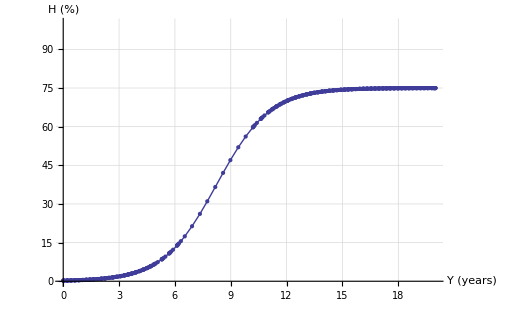

```mathematica
vcr[t_]=75/(1+316.75*Exp[-0.699*t]);
Plot[vcr[t],{t,0,20},AxesLabel->{Style["Y (years)",14,Bold],Style["H (%)",14,Bold]},AxesOrigin->{0,0},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],PlotRange->{0,100},AspectRatio->1/GoldenRatio]
```

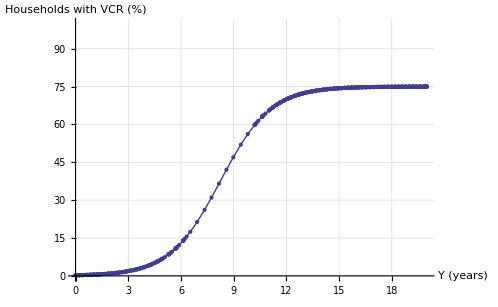

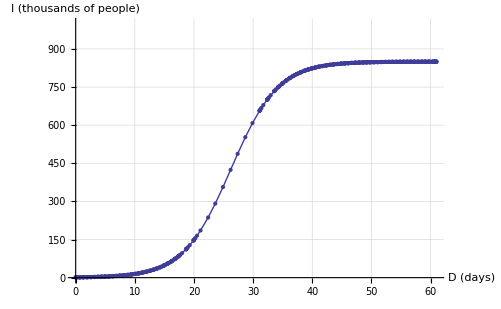

```mathematica
flu[t_]=850/(1+700*Exp[-0.25*t]);
Plot[flu[t],{t,0,61},AxesLabel->{Style["D (days)",14,Bold],Style["I (thousands of people)",14,Bold]},AxesOrigin->{0,0},Mesh->All,PlotStyle->{Thick},LabelStyle->Directive[18],GridLines->Automatic,GridLinesStyle->Directive[Dashed,Black],PlotRange->{0,1000},AspectRatio->1/GoldenRatio]
```